# Gamma-Ray Burst

Hilkar Val Soberanes Soberanes

Wolfram - Data Science Boot Camp

Abstract:
The gamma ray burst are the most powerful kind of explosion known in the entire universe, for years astrophysicists have devised theories of what could produce such an energetic event but our understanding of these electromagnetic phenomenon is still short. Perhaps the analysis of the data from The Second Swift Burst Alert Telescope Gamma-Ray Burst Catalog by using machine learning to find two clusters and fitting a model to one of the cluster  could help to clear our knowledge of the celestial objects which produce this bursts.

## What are GRBs?

According to NASA, gamma-ray bursts (GRBs) are short-lived bursts of gamma-ray light, the most energetic form of light. Lasting anywhere from a few milliseconds to several minutes, GRBs shine hundreds of times brighter than a typical supernova and about a million trillion times as bright as the Sun. When a GRB erupts, it is briefly the brightest source of cosmic gamma-ray photons in the observable Universe.

Search GRBs images on the web:

```mathematica
ImageCollage[WebImageSearch["Gamma-Ray Burst"][[{1,3,5}]]] (* Choose favorite ones and make an Image Collage*)
```

-Graphics-

The reason why GRBs are so energetic it’s because they emit photons on the highest frequency of the electromagnetic spectrum and according to Quantum Physics, the energy of a photon is  directly proportional to the frequency with which it is emitted.

Search for Electromagnetic Spectrum images:

```mathematica
WebImageSearch["Electromagnetic Spectrum"][[2]](*The second one looks better*)
```

-Graphics-

This physical phenomenon involves many branches of physics, from extragalactic astrophysics to quantum mechanics,  that’s what makes it so hard to understand it fully, some of the key ideas to study GRBs can be found on the Wikipedia article about them.

Create a WordCloud from WikipediaData about GRBs:

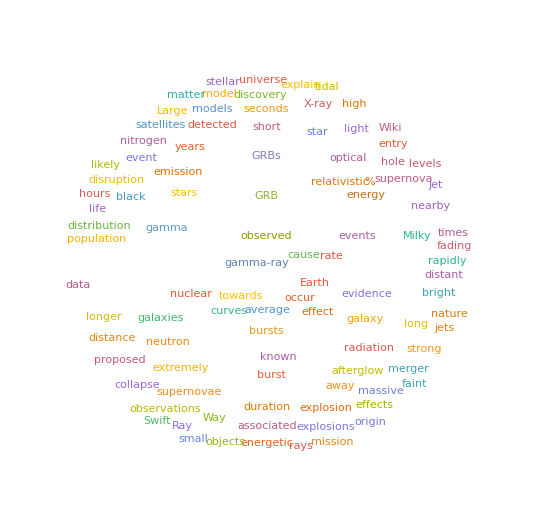

```mathematica
WordCloud[WikipediaData["Gamma Ray Burst"], ColorNegate[Graphics[Disk[]]]]
```

## The Second Swift Burst Alert Telescope Gamma-Ray Burst Catalog

Between 2004 December 19 and 2009 December 21 the Burst Alert Telescope (BAT) mapped the universe looking for Gamma Ray Burst and as a result it provided a catalog containing 476 burst (Sakamoto et al. 2011).  The measurements from each Gamma-Ray Burst event are available on  Wolfram Data Repository and it’s ready for computation using Wolfram Language since all the measurement are in an Entity form.

### Data

Download data from the repository:

```mathematica
raw = ResourceData["The Second Swift Burst Alert Telescope Gamma-Ray Burst Catalog"]
```

Dataset[<>]

Since the dataset structure is associations of associations we can’t use Keys to obtain columns name which are the BAT measurements, so we choose to use First instead:

```mathematica
First@raw (*First row*)
```

#### What can we learn from the data?

Now that we now the measurements made by BAT  we are in position to make some questions related to this variables so we can begin to understand the physical nature of Gamma-Ray Burst just like:

Where do GRBs come from?

The location in the night sky of this kind of events can allow the astronomers to make observations of how that region of the universe evolves after the burst.

How often are GRBs happening?

To know the rate of possible GRBs in a certain unit of time can give us an idea of how common are the  astrophysical systems that produce this kind of event in the universe.

How can we classify GRBs using Machine Learning?

Maybe Machine Learning techniques to classify this objects can help us to see something that traditional methods didn’t yet.

What is relation between the duration and the energy released by a GRB?

Understanding how the energy is released in these kind of systems can help to refine our physical theories.

#### Wrangle

In order to find the answer to our questions we first have to select to variables that are of interest for our study so first we create a dataset called “location” which contains the Declination an Right Ascension of each GRB, these coordinates are analogues to longitude and  latitude since in astronomy the coordinates of the sky are a projection of the conventional geographical coordinates used in earth.

Create location dataset and delete missing data:

```mathematica
location = DeleteCases[raw[All, {"XRTDeclination", "XRTRightAscension"}], <|___,_->_Missing,___|>] (*Delete the assocation that matches the given pattern*)
```

For the time and energy variables we choose to create a dataset called “workingData” which contains the Burst Duration of the 5 to 95 percent of the energy fluence, the energy fluence  detected in the range of energy of 15 to 150 keV, the peak of the rate of energy flux per second in the same range of energy and the date when the observation began. But first we need to remove the missing data an make sure that the units of these measurements have equivalent units.

Create cleanData dataset and delete missing data and the data with errors:

```mathematica
cleanData=DeleteCases[raw[All, {"BurstDuration5To95PercentOfFluence", "EnergyFluence15To150keV", "OneSecondPeakEnergyFlux15To150keV", "TriggerTime"}], <|___,_->_Missing,___|>|<|_->{_,_}, ___|>](*Delete the assocation that matches the given pattern*)
```

Now that the data is clean we observe that the energy fluence is in femto Joules over centimeter square, while the peak of the rate of energy flux per second is in watts over meter square so in order for them to be equivalent we use UnitConvert to convert the peak of the rate of energy flux per second  into femto Watts over centimeter square.

Create workingData dataset with equivalent units

```mathematica
workingData =Block[{data = #},data["OneSecondPeakEnergyFlux15To150keV"]=UnitConvert[data["OneSecondPeakEnergyFlux15To150keV"], "Femtowatts"/("Centimeters"^2)]; data]&/@cleanData
```

### Visualization

Now that the data is clean, we can begin to explore it in order to find, or not find, the answer to our questions.

#### Where do GRBs come from?

Like we said the astronomical coordinates are a projection of geographical coordinates on earth so we can use GeoProjection to make a proper GeoGraphics of the “location” data, which becomes very easy thanks to GeoPosition that automatically converts right ascension to  degrees.

Graph location of the GRBs in the catalog specifying astronomical coordinates:

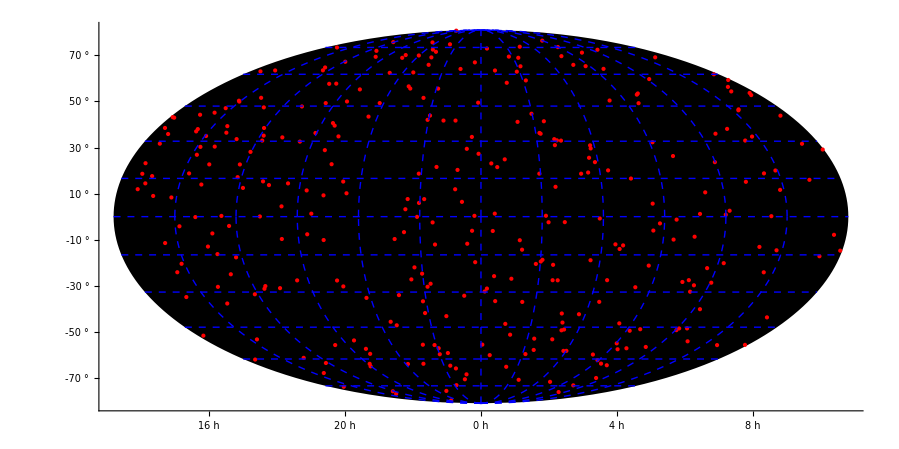

```mathematica
GeoGraphics[{Red, Point[Values[GeoPosition[#]&/@location[All, Values]]]}, GeoProjection->"Mollweide", GeoRange->"World", GeoBackground->Black, GeoGridLines->Automatic, GeoGridLinesStyle->Directive[Dashed,Blue], Axes->True,Ticks->{Table[{N[i Degree],Row[{Mod[i/15+24,24]," h"}]},{i,-180,180,30}],Table[{N[i Degree],Row[{i," °"}]},{i,-90,90,10}]}]
```

The previous visualization allow us to have a global idea of how the GRBs in the catalog are distributed across the universe, perhaps the random distribution observed  in it tell no much for the reader but an astronomer or even a amateur astronomer familiarized with astronomical coordinates can look at this map an have a global idea of where to look for the remaining of a GRB system. Without any doubt try to find one of these points in a telescope could become a great experience for anyone.

#### How often are GRBs happening?

Since the dataset “workigData” provides the date when the observation of each Gamma-Ray Burst began in the catalog we can make a Table which contains al dates as a DateObject and use it to generate a DateHistogram of the total GRBs detected per year.

Generate DateHistrogram by Year:

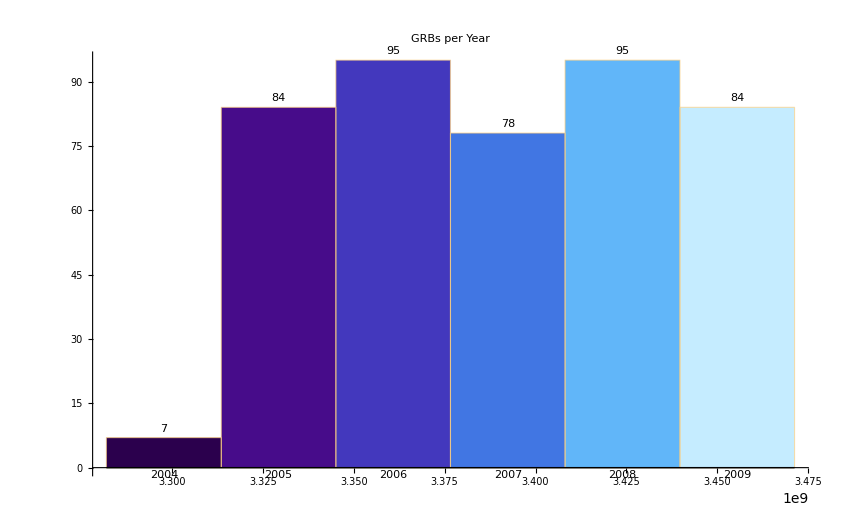

```mathematica
dates= Table[workingData[row, "TriggerTime"], {row, Length[workingData]}];
DateHistogram[dates, "Year", ChartStyle->"DeepSeaColors", PlotLabel->"GRBs per Year", LabelingFunction->Above]
```

It looks like the GRBs have a very uniform distribution during the detection years, since the detections started on December 2004 we can’t say much about that year so we will just consider the following year for making a Grid of statistical analysis of the number of GRBs per year.

Create grid with Mean, Median, Min, Max and Standard Deviation:

```mathematica
Grid[{{"Statistic", "GRBs per Year" },{"Mean", Mean[#1]},{"Median", Median[#1]}, {"Min", Min[#1]}, {"Max", Max[#1]}, {"Standard Deviation", StandardDeviation[#1]}}, Frame->All, Alignment->Left, Spacings->{2,2}]&@N[Counts[DateValue[#, "Year"]&/@dates][[2;;]]]
```

Statistic | GRBs per Year
Mean | 87.2
Median | 84.
Min | 78.
Max | 95.
Standard Deviation | 7.52994

Therefore we can say no just that Gamma-Ray Burst are distributed all across the universe but also are happening very frequently at least 78 and up to 96 detections of these electromagnetic phenomenon per year, this make us infer that the astrophysical systems responsible for the burst are quite abundant in the universe.

#### How can we classify this events?

Having a general idea of the answer of our first two questions, we can now move to the third one, let’s see a graphical representation of the more specific measurements of each GRB, the burst duration from 5 to 95 percent of it energy fluence, the one second peak of energy flux  in the range of energy 15 to 150 keV (maximum energy detected in one second per unit of surface)and the energy fluence in the same range (total energy detected per unit of surface); for this we use a BubbleChart a way to visualize three dimensional data on a plane.  Given the large amount of data with measurements in a wide range of magnitudes, we have chosen to make this visualization using a logarithmic scale in order to better distinguish the bubbles.

Create a table for the measurements we are going to work in this section:

```mathematica
measurements=Table[workingData[row,col], {row, Length[workingData]}, {col, {"BurstDuration5To95PercentOfFluence", "OneSecondPeakEnergyFlux15To150keV",  "EnergyFluence15To150keV"}}] (*Table with the data we are interested in*)
```

{{5.65 s,54.2 fW/cm^2,270. fJ/cm^2},{10. s,16.3 fW/cm^2,114. fJ/cm^2},{5.58 s,14.5 fW/cm^2,36.6 fJ/cm^2},{109.08 s,74.6 fW/cm^2,1700. fJ/cm^2},{177.17 s,24.9 fW/cm^2,853. fJ/cm^2},{89.5 s,2.94 fW/cm^2,31. fJ/cm^2},{52.16 s,11.4 fW/cm^2,345. fJ/cm^2},{166.65 s,21.9 fW/cm^2,867. fJ/cm^2},{3.93 s,46.6 fW/cm^2,118. fJ/cm^2},{48. s,4.22 fW/cm^2,88. fJ/cm^2},{28. s,61.6 fW/cm^2,511. fJ/cm^2},{0.11 s,4.46 fW/cm^2,3.16 fJ/cm^2},{66.41 s,5.02 fW/cm^2,63.9 fJ/cm^2},{10.62 s,4.47 fW/cm^2,23.5 fJ/cm^2},{23.84 s,31.4 fW/cm^2,408. fJ/cm^2},{28.74 s,184. fW/cm^2,1580. fJ/cm^2},{21.68 s,5. fW/cm^2,64.6 fJ/cm^2},{158.43 s,30.4 fW/cm^2,1140. fJ/cm^2},{95.57 s,11.3 fW/cm^2,317. fJ/cm^2},{151.74 s,8.92 fW/cm^2,133. fJ/cm^2},{29.44 s,117. fW/cm^2,884. fJ/cm^2},{33.3 s,99.2 fW/cm^2,831. fJ/cm^2},{4.79 s,2.04 fW/cm^2,6.7 fJ/cm^2},{64. s,10.7 fW/cm^2,435. fJ/cm^2},{26.46 s,5.42 fW/cm^2,62.9 fJ/cm^2},{6.62 s,19.9 fW/cm^2,40.7 fJ/cm^2},{3.4 s,57.3 fW/cm^2,111. fJ/cm^2},{81.78 s,33.4 fW/cm^2,511. fJ/cm^2},{11.04 s,3.1 fW/cm^2,14.3 fJ/cm^2},{80. s,1.76 fW/cm^2,59.6 fJ/cm^2},{16.62 s,10.7 fW/cm^2,47.1 fJ/cm^2},{58.88 s,16.7 fW/cm^2,251. fJ/cm^2},{11.39 s,5.19 fW/cm^2,33.6 fJ/cm^2},{0.02 s,1.82 fW/cm^2,0.71 fJ/cm^2},{8.84 s,338. fW/cm^2,1510. fJ/cm^2},{10.08 s,9.11 fW/cm^2,44.7 fJ/cm^2},{22. s,158. fW/cm^2,703. fJ/cm^2},{48. s,1.55 fW/cm^2,61.2 fJ/cm^2},{30.4 s,22.5 fW/cm^2,136. fJ/cm^2},{51.61 s,3.42 fW/cm^2,109. fJ/cm^2},{94.91 s,38.6 fW/cm^2,505. fJ/cm^2},{122.03 s,13.6 fW/cm^2,432. fJ/cm^2},{46.87 s,3.4 fW/cm^2,52.7 fJ/cm^2},{49.62 s,7.3 fW/cm^2,138. fJ/cm^2},{69.02 s,16.8 fW/cm^2,615. fJ/cm^2},{77.84 s,57.1 fW/cm^2,634. fJ/cm^2},{94.37 s,15.1 fW/cm^2,361. fJ/cm^2},{99.14 s,23.9 fW/cm^2,101. fJ/cm^2},{49.7 s,12.7 fW/cm^2,197. fJ/cm^2},{145.05 s,4.61 fW/cm^2,237. fJ/cm^2},{19.4 s,11.7 fW/cm^2,30.8 fJ/cm^2},{27.46 s,22.1 fW/cm^2,221. fJ/cm^2},{88.12 s,8.14 fW/cm^2,217. fJ/cm^2},{0.45 s,4.21 fW/cm^2,3.65 fJ/cm^2},{144. s,2.56 fW/cm^2,195. fJ/cm^2},{2.38 s,3.87 fW/cm^2,7.88 fJ/cm^2},{37.72 s,2.6 fW/cm^2,30.6 fJ/cm^2},{12.06 s,36.5 fW/cm^2,205. fJ/cm^2},{104.12 s,13.9 fW/cm^2,248. fJ/cm^2},{24.82 s,3.29 fW/cm^2,27.3 fJ/cm^2},{35.73 s,3.17 fW/cm^2,42. fJ/cm^2},321,{56.31 s,15.8 fW/cm^2,466. fJ/cm^2},{8.47 s,14.1 fW/cm^2,23.7 fJ/cm^2},{9.77 s,12.4 fW/cm^2,62.5 fJ/cm^2},{49.47 s,580. fW/cm^2,2180. fJ/cm^2},{1.24 s,15.7 fW/cm^2,18.5 fJ/cm^2},{184. s,4.97 fW/cm^2,109. fJ/cm^2},{5.61 s,10.3 fW/cm^2,32.9 fJ/cm^2},{336.38 s,12.2 fW/cm^2,331. fJ/cm^2},{5.66 s,43.2 fW/cm^2,61.7 fJ/cm^2},{0.04 s,2.77 fW/cm^2,2.23 fJ/cm^2},{208. s,12.8 fW/cm^2,917. fJ/cm^2},{85.82 s,18. fW/cm^2,65.6 fJ/cm^2},{58.26 s,6.88 fW/cm^2,118. fJ/cm^2},{40.46 s,26.6 fW/cm^2,109. fJ/cm^2},{42.8 s,11. fW/cm^2,154. fJ/cm^2},{55. s,16.8 fW/cm^2,61.3 fJ/cm^2},{2.29 s,5.91 fW/cm^2,11.4 fJ/cm^2},{113.34 s,310. fW/cm^2,10900. fJ/cm^2},{0.14 s,6.84 fW/cm^2,7.32 fJ/cm^2},{24.95 s,11.3 fW/cm^2,90.4 fJ/cm^2},{8.7 s,8.36 fW/cm^2,50.1 fJ/cm^2},{88.73 s,71.6 fW/cm^2,2530. fJ/cm^2},{27.02 s,18.4 fW/cm^2,147. fJ/cm^2},{186.68 s,6.87 fW/cm^2,388. fJ/cm^2},{64. s,4.82 fW/cm^2,95.2 fJ/cm^2},{265.39 s,31.1 fW/cm^2,567. fJ/cm^2},{3. s,20. fW/cm^2,88.3 fJ/cm^2},{56.68 s,4.09 fW/cm^2,78.7 fJ/cm^2},{301.87 s,4.43 fW/cm^2,142. fJ/cm^2},{64. s,3.15 fW/cm^2,109. fJ/cm^2},{146.36 s,4.68 fW/cm^2,218. fJ/cm^2},{7.84 s,8.63 fW/cm^2,36.5 fJ/cm^2},{75.09 s,35.3 fW/cm^2,573. fJ/cm^2},{7.14 s,70.1 fW/cm^2,133. fJ/cm^2},{78.22 s,4.28 fW/cm^2,127. fJ/cm^2},{0.58 s,4.77 fW/cm^2,4.47 fJ/cm^2},{8. s,7.7 fW/cm^2,119. fJ/cm^2},{77.95 s,4.76 fW/cm^2,38.1 fJ/cm^2},{129.53 s,13.1 fW/cm^2,289. fJ/cm^2},{64. s,17.8 fW/cm^2,1270. fJ/cm^2},{135.52 s,9.61 fW/cm^2,448. fJ/cm^2},{9.6 s,9.65 fW/cm^2,60.5 fJ/cm^2},{62.45 s,15.2 fW/cm^2,93.8 fJ/cm^2},{99.28 s,27.2 fW/cm^2,713. fJ/cm^2},{2.16 s,13.2 fW/cm^2,19.8 fJ/cm^2},{361.6 s,31.4 fW/cm^2,582. fJ/cm^2},{4.37 s,54. fW/cm^2,143. fJ/cm^2},{38.92 s,36.5 fW/cm^2,380. fJ/cm^2},{112.28 s,18.5 fW/cm^2,598. fJ/cm^2},{174. s,18.7 fW/cm^2,203. fJ/cm^2},{39.18 s,10.9 fW/cm^2,241. fJ/cm^2},{6.65 s,13.1 fW/cm^2,52.5 fJ/cm^2},{107.14 s,3.4 fW/cm^2,76.1 fJ/cm^2},{48.03 s,9.93 fW/cm^2,164. fJ/cm^2},{0.27 s,19.6 fW/cm^2,19.5 fJ/cm^2},{19.59 s,18.2 fW/cm^2,209. fJ/cm^2},{0.384 s,26.3 fW/cm^2,43.2 fJ/cm^2},{7.42 s,273. fW/cm^2,844. fJ/cm^2},{130.91 s,9.35 fW/cm^2,146. fJ/cm^2},{80. s,5.3 fW/cm^2,180. fJ/cm^2},{14.8 s,112. fW/cm^2,320. fJ/cm^2}}
 |  |  |  |

Choose the color of the bubbles:

```mathematica
colors = ColorData[{"DeepSeaColors", "Reverse"}]; (*The Color Fuction of the Bubbles*)
```

Generate a Bubble chart using the “measurements” table and the Color Function “colors”:

```mathematica
chart1=BubbleChart[measurements, ScalingFunctions->{"Log", "Log"},FrameLabel->{"Burst Duration 5 To 95 Percent Of Fluence (seconds)", "One Second Peak Energy Flux 15 To 150 keV"}, ColorFunction->Function[{x,y,z},colors[z]], ChartLegends-> BarLegend[{{"DeepSeaColors", "Reverse"},QuantityMagnitude[MinMax[workingData[All, 2]]]},LegendLabel->Placed["Energy Fluence 15 To 150 keV",Right,Rotate[#,90Degree]&]], ImageSize->400, PlotLabel->"GRB Duration vs One Second Peak Energy Flux vs Energy Fluence"]
```

-Graphics-

This chart let us see the relation between the duration and the way that the energy is  released in the Gamma-Ray Bursts, however the high density of bubbles in it makes it hard to find an obvious  classification  for them.  Therefore we proceed to visualize the distribution of each of this measurements making a GraphicsGrid of a Table of Histograms of each one of them.   The histograms are also in a logarithmic scale in order to distinguish the distributions.

Generate a Grid of Histograms for each measurement using the list of measurements names for the titles:

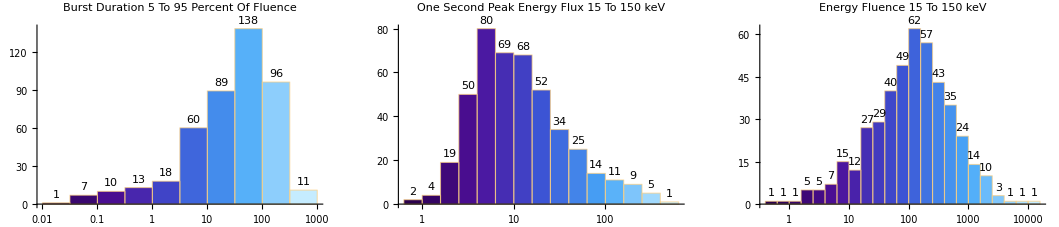

```mathematica
measurementsNames= {"Burst Duration 5 To 95 Percent Of Fluence", "One Second Peak Energy Flux 15 To 150 keV",  "Energy Fluence 15 To 150 keV"}; (*Titles of the Histograms*)
GraphicsGrid[{Table[Histogram[measurements[[All, i]],"Log", ChartStyle->"DeepSeaColors", PlotLabel->measurementsNames[[i]], LabelingFunction->Above], {i, 1,3}]}](*It.b4s recommended to make the grid bigger for a better visualization*)
```

We observe that each measurement has its own distribution, while the burst duration appears to have a gamma distribution, the energy fluence appears to have a normal distribution, so now we will continue to explore the data by summarising the statistics of these measurements in the following grid.

Create Grid with Mean, Median, Maximum, Minimum and Standard Deviation of each variable:

```mathematica
Grid[Join[{{"Measurement","Mean", "Median", "Maximum", "Minimum", "Standard Deviation"}},Table[{measurementsNames[[i]],Mean[measurements[[All, i]]], Median[measurements[[All, i]]], Max[measurements[[All, i]]], Min[measurements[[All, i]]], StandardDeviation[measurements[[All, i]]]}, {i,1,3}]], Frame->All,  Alignment->Left, Spacings->{2,2}]
```

Measurement | Mean | Median | Maximum | Minimum | Standard Deviation
Burst Duration 5 To 95 Percent Of Fluence | 69.1008 s | 41.37 s | 539.12 s | 0.02 s | 82.5129 s
One Second Peak Energy Flux 15 To 150 keV | 27.0553 fW/cm^2 | 9.93 fW/cm^2 | 580. fW/cm^2 | 0.68 fW/cm^2 | 54.7707 fW/cm^2
Energy Fluence 15 To 150 keV | 336.224 fJ/cm^2 | 124. fJ/cm^2 | 10900. fJ/cm^2 | 0.61 fJ/cm^2 | 801.917 fJ/cm^2

Despite the different visualizations of the data and distributions observed for each variable that have already provide us with a global idea of the answers that we could obtain to our research questions it is needed further analysis in order to be able to obtain a clear relation between the duration of GRBs and the way that they release their energy. As we can see in the previous grid, the measurements made by the BAT telescope are in a very wide range, what make us infer that there are different kind of astrophysical objects that produce this kind of burst.   Perhaps using machine learning for finding clusters in the data will allow us to obtain better visualizations with a more clear relation between the variables.

## Analysis

### Classification

In order to find different classifications for the GRBs detections we use the machine learning function FindClusters with the performance goal of Quality to find the best partition of the data.

Create a list called clusters with the clusters found by  FindClusters:

```mathematica
clusters= FindClusters[measurements, PerformanceGoal->"Quality"];
Length[clusters](*Find the number of clusters*)
```

2

Find the length of each cluster:

```mathematica
Map[Length, clusters]
```

{79,364}

Now that we have two cluster with 79 and 364 data points respectively we can generate a bubble chart similar to the previous one but that allow us to distinguish each cluster.

Create BubbleChart of the clusters list:

```mathematica
chart2 =BubbleChart[clusters, ScalingFunctions->{"Log", "Log"},FrameLabel->{"Burst Duration 5 To 95 Percent Of Fluence (seconds)", "One Second Peak Energy Flux 15 To 150 keV"}, ChartLegends->Table[Row[{"Cluster", i}],{i, Length[clusters]}], ChartStyle->{Red, Green}, ImageSize->400, PlotLabel->"GRB Duration vs One Second Peak Energy Flux vs Energy Fluence"]
```

-Graphics-

In order to have this classification of the data we can repeat the visualizations of the distribution of each measurement first for the Cluster 1.

Generate a Grid of Histograms for each measurement in the first cluster using the list of measurements names for the titles:

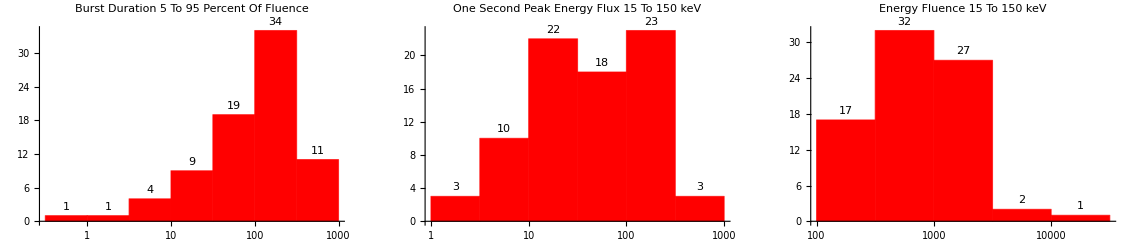

```mathematica
GraphicsGrid[{Table[Histogram[clusters[[1]][[All, i]],"Log",ChartStyle->Red, PlotLabel->measurementsNames[[i]], LabelingFunction->Above], {i, 1, 3}]}](*It.b4s recommended to make the grid bigger for a better visualization*)
```

In the same way we can make a grid summarizing the statistics of this cluster.

Create grid with Mean, Median, Maximum, Minimum and Standard Deviation for the first cluster:

```mathematica
Grid[Join[{{"Measurement","Mean", "Median", "Maximum", "Minimum", "Standard Deviation"}},Table[{measurementsNames[[i]],Mean[clusters[[1]][[All, i]]], Median[clusters[[1]][[All, i]]], Max[clusters[[1]][[All, i]]], Min[clusters[[1]][[All, i]]], StandardDeviation[clusters[[1]][[All, i]]]}, {i,1,3}]], Frame->All,  Alignment->Left, Spacings->{2,2}]
```

Measurement | Mean | Median | Maximum | Minimum | Standard Deviation
Burst Duration 5 To 95 Percent Of Fluence | 160.638 s | 124.86 s | 539.12 s | 0.74 s | 129.961 s
One Second Peak Energy Flux 15 To 150 keV | 89.9787 fW/cm^2 | 52.5 fW/cm^2 | 580. fW/cm^2 | 1.22 fW/cm^2 | 105.798 fW/cm^2
Energy Fluence 15 To 150 keV | 1195.37 fJ/cm^2 | 815. fJ/cm^2 | 10900. fJ/cm^2 | 105. fJ/cm^2 | 1615.66 fJ/cm^2

Now we repeat the procedure for the second cluster.

Generate a Grid of Histograms for each measurement in the second cluster using the list of measurements names for the titles:

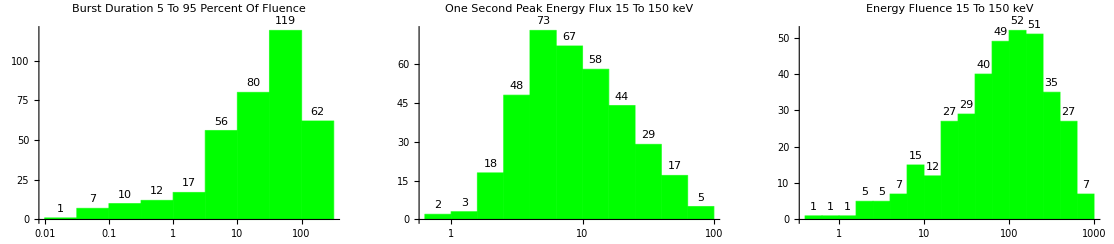

```mathematica
GraphicsGrid[{Table[Histogram[clusters[[2]][[All, i]],"Log",ChartStyle->Green, PlotLabel->measurementsNames[[i]], LabelingFunction->Above], {i, 1, 3}]}](*It.b4s recommended to make the grid bigger for a better visualization*)
```

```mathematica
Grid[Join[{{"Measurement","Mean", "Median", "Maximum", "Minimum", "Standard Deviation"}},Table[{measurementsNames[[i]],Mean[clusters[[2]][[All, i]]], Median[clusters[[2]][[All, i]]], Max[clusters[[2]][[All, i]]], Min[clusters[[2]][[All, i]]], StandardDeviation[clusters[[2]][[All, i]]]}, {i,1,3}]], Frame->All,  Alignment->Left, Spacings->{2,2}]
```

Measurement | Mean | Median | Maximum | Minimum | Standard Deviation
Burst Duration 5 To 95 Percent Of Fluence | 49.2343 s | 30.75 s | 209.24 s | 0.02 s | 49.4124 s
One Second Peak Energy Flux 15 To 150 keV | 13.3988 fW/cm^2 | 8.695 fW/cm^2 | 86.9 fW/cm^2 | 0.68 fW/cm^2 | 14.1011 fW/cm^2
Energy Fluence 15 To 150 keV | 149.762 fJ/cm^2 | 90.8 fJ/cm^2 | 915. fJ/cm^2 | 0.61 fJ/cm^2 | 163.144 fJ/cm^2

This analysis has give us an statistical understanding of the main difference between this two clusters, we observe that the main cluster contain no just burst with a higher duration but also a higher energy fluence and higher one second peak of energy flux than the second one. Usually the astronomers that study this kind of events classify them in long GRBs for those with a duration higher that two seconds and  short GRBs for those with a duration less than two seconds, but we observe that this is not the case in this classification since the minimum burst duration in the first cluster is 0.74 seconds which means the classification made by the function  FindClusters is a non traditional way to analyse this kind of data.

### Model Fitting

#### What is relation between the duration and the energy released by a GRB?

Now that we have two main classifications in our data we can try find a correlation between the measurements we have been working, for example we can make a visualization of the first cluster without using a logarithmic scale.

Create a BubbleChart of the first cluster, using normal scale:

```mathematica
chart3 =BubbleChart[clusters[[1]], FrameLabel->{"Burst Duration 5 To 95 Percent Of Fluence (seconds)", "One Second Peak Energy Flux 15 To 150 keV"}, ChartStyle->Red, PlotLabel->"GRB Duration vs One Second Peak Energy Flux vs Energy Fluence",ImageSize->400,  ChartLegends->{"Cluster 1"}]
```

-Graphics-

We observe an asymptotic behavior between the Burst Duration and the One Second Peak of Energy Flux, which physically means that the burst duration is inversely proportional to the rate with which it release its energy , in other words, the faster the energy release, the shorter the burst duration. The size of the bubbles also help us to understand this kind of behavior since the bigger bubbles aren’t the one that last longer.  Now we propose a non linear fit in order to check this behavior.

Find Non Linear  Model Fit for the data from cluster 1:

```mathematica
cluster1NumericData =QuantityMagnitude[clusters[[1]][[All,;;2]]]; (*Obtains the numerical magnitud of the data*)
nlm = NonlinearModelFit[cluster1NumericData, a/Log[x], a, x]
```

FittedModel[76.0932/Log[x]]

```mathematica
Normal[nlm](*Formula from the found model*)
```

76.0932/Log[x]

Visualization of the model:

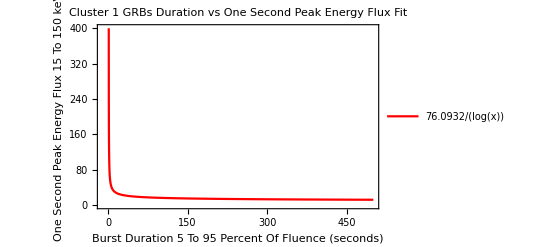

```mathematica
chart4 =Plot[nlm[x], {x, 0,500},  PlotStyle->{Red, Thick}, Frame->True, FrameLabel->{"Burst Duration 5 To 95 Percent Of Fluence (seconds)", "One Second Peak Energy Flux 15 To 150 keV"}, PlotRange->{{-10,500},{0,400}}, PlotLabel->"Cluster 1 GRBs Duration vs One Second Peak Energy Flux Fit",ImageSize->400, PlotLegends->LineLegend[{Red}, {Normal[nlm]}]]
```

Show the model with the data in the same plot:

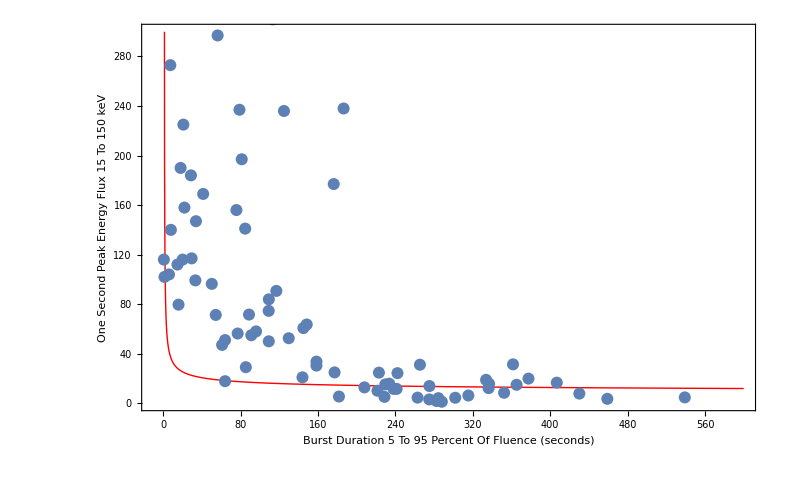

```mathematica
Show[Plot[nlm[x], {x, 0, 600}, PlotStyle->{Red, Thick}, Frame->True, FrameLabel->{"Burst Duration 5 To 95 Percent Of Fluence (seconds)", "One Second Peak Energy Flux 15 To 150 keV"}, PlotRange->{{-10, 600}, {0,300}}],ListPlot[cluster1NumericData]]
```

See graphically the fit  residuals:

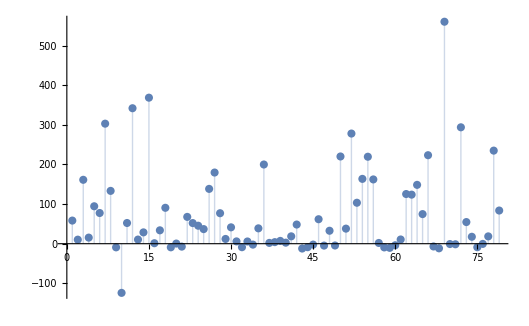

```mathematica
ListPlot[nlm["FitResiduals"], Filling->Axis]
```

We observe that the model fitted is not perfect for the description of the data since there are big residuals however the qualitative behavior of the data agrees with the kind of model we tried to fit so we can say that there is a relation of inverse proportionality between the burst duration and the one second peak energy flux which answers our last question at least for the first cluster. Now lets see what happens in the case of the second cluster.

BubbleChart of the second cluster using normal scale:

```mathematica
BubbleChart[clusters[[2]], FrameLabel->{"Burst Duration 5 To 95 Percent Of Fluence (seconds)", "One Second Peak Energy Flux 15 To 150 keV"}, ChartStyle->Green]
```

-Graphics-

We observe that the dispersion of data bubbles is to high to try to fit a model like we did for the previous cluster, but we can observe qualitatively the same kind of behavior asymptotic between the burst duration and the one second peak energy flux.

## Conclusion

Using the data from The Second Swift Burst Alert Telescope Gamma-Ray Burst Catalog obtained from the   Wolfram Data Repository we were able to answer some interesting questions about this kind of events that are characterized by being the most powerful explosions known in the universe. From the exploration of the data, it was possible to identify its position in a geographical projection to know where these phenomena came from and the frequency with which these types of events occur was also found, given an average of 72 of these events per year.  Also through a more in-depth analysis using Machine Learning to identify clusters from physical measurements related to the duration and energy release of each GRB it was possible to distinguish two clusters and by graphing them separately, an inverse proportionality relationship was identified. between the selected variables. We thus conclude that the analysis techniques used in this project, despite being different from those used by (Sakamoto et al. 2011), have yielded results that could serve for a better understanding of the astrophysical systems that generate the GRBs

```mathematica
infographic =GraphicsGrid[{{chart1,chart2}, {chart3, chart4}}]
```

-Graphics-

## Keywords

Gamma Ray

Burst

Astrophysics

Clusters

NonLinearModelFit

## References

Sakamoto, Takanori & Barthelmy, Scott & Baumgartner, Wayne & Cummings, Jay & Fenimore, E. & Gehrels, Neil & Krimm, Hans & Markwardt, Craig & Palmer, David & Parsons, Ann & Sato, G. & Stamatikos, Michael & Tueller, J. & Ukwatta, T. & Zhang, and. (2011). The Second Swift Burst Alert Telescope Gamma-Ray Burst Catalog. The Astrophysical Journal Supplement Series. 195. 2. 10.1088/0067-0049/195/1/2.  Available at:  https://www.researchgate.net/publication/230957728_The _Second _Swift _Burst _Alert _Telescope _Gamma-Ray_Burst _Catalog

Wolfram Research, “The Second Swift Burst Alert Telescope GammaRay Burst Catalog” from the Wolfram Data Repository (2017) Available at: https://doi.org/10.24097/wolfram.34168.data